## SFT calculations and asymptotics

This document explores and benchmarks the exact integration of the Fourier transform on the ARM sphere of a simple but suitable model of a molecular orbital which works well for simple di- and tri-atomic molecules. The form factor R(p) of the ARM formalism can be expressed in terms of such a transform, which can be written as

            SFT(q)=∫dΩ/(2π)e^(-ⅈ q·r̂)F(r̂),
where F(r̂) is the angular part of the Dyson orbital, i.e. ⟨r|n_D⟩=C_κ κ^(3/2)(ⅇ^(-κ r)(κ r))^(Q/κ-1)F(r̂). This angular dependence can be modelled well, by all accounts, as

            F(r̂)=cosh(b cos (θ))(1+c cos^2(θ))cos^N_z(θ) sin^(N_x+N_y)(θ) cos^N_x(ϕ)sin^N_y(ϕ).

This model is taken from a paper by Murray et al. (PRL 106 173001), which cites in turn A.A. Radzig and B. M. Smirnov, Reference data on atoms, molecules and ions (Springer-Verlag, Berlin, 1985), as a source for that form.

This integral can be done exactly, as explained in the thesis, by turning the cosh into exponentials and using standard special-functions theory (specifically, Gegenbauer’s finite integral, in Watson’s Bessel functions book, p. 50, or formulas 7.333.1 and .2 in Gradshteyn and Ryzhik). It comes out to the very nice form

            SFT(q)=(-ⅈ)^N_xyz∑_± (q_x^N_x(q_y^N_y(q_z±ⅈ b))^N_z)/((q_x^2+q_y^2+(q_z±ⅈ b)^2)^(N_xyz/2))[(1+c (N_z+1/2)/(N_xyz+3/2))j_N_xyz(√(q_x^2+q_y^2+(q_z±ⅈ b)^2))-c((q_z±ⅈ b)^2/(q_x^2+q_y^2+(q_z±ⅈ b)^2)-(N_z+1/2)/(N_xyz+3/2))j_(N_xyz+2)(√(q_x^2+q_y^2+(q_z±ⅈ b)^2))],
            
where the js are spherical Bessel functions and N_xyz=N_x+N_y+N_z.

One curious feature is that SFT(q) is only a function of the transverse momentum. This is because, by definition, q=a(p+A(t_s)), and t_s itself is a function of the momentum, through the saddle-point equation 1/2(p+A(t_s))+I_p=0, which can also be written as p_∥+A(t_s)=-ⅈ √(κ^2+p_⊥^2), and therefore q=a(p_⊥-ⅈ √(κ^2+p_⊥^2)n̂).


This document also contains some derived functions which help make sense of this solution.
   • An approximation to SFT in the case of large a and small tunnelling angles, which to leading order reads
 SFT(q)≃(-ⅈ)^N_xyz ⅇ^(κ a)/(κ a)(v_x^n_x v_y^n_y v_z^n_z)/κ^(n_x+n_y+n_z)cos(b(p_o/κ sin(θ)+ⅈ (1+(p_⊥^2)/(2 κ^2))cos(θ)))×(1+c(p_o^2/κ^2 cos(2θ)+(1+p_y^2/κ^2)cos^2(θ)-ⅈ/2 √(1+(p_⊥^2)/(2 κ^2))p_o/κ sin(2θ))).
   • Systematic refinements of this asymptotic approximation to higher order in 1 /κa.
    
   • Restricted versions of SFT for the case of on-axis ionization, or slight variations. Specifically, there are simpler expressions available for the case of SFT(p_⊥=0), and for its derivatives with respect to p_o and p_ythere. These are useful because they can be used to approximate it as SFT(q)=SFT(p_⊥=0)+q_o∂/(∂q_o)SFT|_(p_⊥=0)+q_y∂/(∂q_y)SFT|_(p_⊥=0), which is the corresponding version of the small-angle approximation that is given in the original single-electron ARM paper (Torlina et al, PRA 86 043409).

## Initialization

```mathematica
Needs["ARMSupport`"]
$ARMSupportVersion
```

ARMSupport v1.0.15, Tue 7 Jun 2016 22:14:23

## Old definitions

### Preliminaries

This assigns the value 1 to the formally undefined expression 0^0, which in this context is always a special case of r^n for real r and integer n. However, it is important to note that this is (in principle) dangerous, and it can potentially cause errors in other notebooks that are running on the same kernel.

```mathematica
Unprotect[Power];
Power[0,0]=1;
Power[0.+0.ⅈ,0]=1;
Power[0.,0]=1;
Protect[Power];
```

Some functions for support. The velocity vector vel at t_sas a function of alignment angle and transverse momentum and the corresponding q vector.

```mathematica
vel[θ_,po_,py_,κ_]:=(po{Cos[θ],0,-Sin[θ]}+py {0,1,0}-ⅈ √(κ^2+po^2+py^2){Sin[θ],0,Cos[θ]});
qvec[a_,θ_,po_,py_,κ_]:=a vel[θ,po,py,κ];
```

### SFTnumeric

#### Old version - not working for some reason

Uses parallelized memoization as per mm.se/q/1259

```mathematica
SFTnumeric[qx_,qy_,qz_,b_,c_,nx_,ny_,nz_]:=With[{result=SFTnumericParallelized[qx,qy,qz,b,c,nx,ny,nz]},(SFTnumeric[qx,qy,qz,b,c,nx,ny,nz]=result)/;result=!=Null];
SFTnumeric[qx_,qy_,qz_,b_,c_,nx_,ny_,nz_]:=SFTnumericParallelized[qx,qy,qz,b,c,nx,ny,nz]=SFTnumeric[qx,qy,qz,b,c,nx,ny,nz]=NIntegrate[
1/(2π)ⅇ^(-ⅈ(qx Sin[θ]Cos[ϕ]+qy Sin[θ]Sin[ϕ]+qz Cos[θ]))Cosh[b Cos[θ]](1+c Cos[θ]^2)Cos[θ]^nz Sin[θ]^(nx+ny+1)Cos[ϕ]^nx Sin[ϕ]^ny
,{θ,0,π},{ϕ,0,2π}
,Method->"MultidimensionalRule"
]
SetSharedFunction[SFTnumericParallelized];
SFTnumeric[{qx_,qy_,qz_},b_,c_,nx_,ny_,nz_]:=SFTnumeric[qx,qy,qz,b,c,nx,ny,nz]
```

#### New version

```mathematica
Quit
```

```mathematica
SFTnumeric[qx_?NumericQ,qy_?NumericQ,qz_?NumericQ,b_,c_,nx_,ny_,nz_]:=With[
{result=SFTnumericParallelized[qx,qy,qz,b,c,nx,ny,nz]},
If[(result===Null&&$KernelID>0)||(Head[result]===SFTnumericParallelized&&$KernelID==0),
SFTnumericParallelized[qx,qy,qz,b,c,nx,ny,nz]=NIntegrate[
1/(2π)ⅇ^(-ⅈ(qx Sin[θ]Cos[ϕ]+qy Sin[θ]Sin[ϕ]+qz Cos[θ]))Cosh[b Cos[θ]](1+c Cos[θ]^2)Cos[θ]^nz Sin[θ]^(nx+ny+1)Cos[ϕ]^nx Sin[ϕ]^ny
,{θ,0,π},{ϕ,0,2π}
,Method->"MultidimensionalRule"
]
,result
]
]
SetSharedFunction[SFTnumericParallelized];
```

```mathematica
AbsoluteTiming[
SFTnumeric[3+ⅈ,0,15,2.5,1,0,0,0]
]
```

{0.93595,0.337514-0.281196 ⅈ}

```mathematica
Column@AbsoluteTiming@Block[{b=2.5,c=1,nx=0,ny=0,nz=0,part=Re[ⅇ^ⅈ#]&},
ParallelTable[
part[SFTnumeric[qx,0,qz,b,c,nx,ny,nz]]
,{qx,-15,15,5},{qz,-15,15,5}
]
]
```

$Aborted

### SFTanalytic

```mathematica
SFTanalytic[qx_,qy_,qz_,b_,c_,nx_,ny_,nz_]:=With[{ss=Function[s,√(qx^2+qy^2+(qz+s ⅈ b)^2)],j=SphericalBesselJ,n=nx+ny+nz},
Sum[(-ⅈ)^(nx+ny+nz)qx^nx qy^ny(qz+s ⅈ b)^nz((1+c (nz+1/2)/(n+3/2))j[n,ss[s]]/ss[s]^n-c((qz+s ⅈ b)^2/(qx^2+qy^2+(qz+s ⅈ b)^2)-(nz+1/2)/(n+3/2))j[n+2,ss[s]]/ss[s]^n),{s,{1,-1}}]
]
SFTanalytic[{qx_,qy_,qz_},b_,c_,nx_,ny_,nz_]:=SFTanalytic[qx,qy,qz,b,c,nx,ny,nz]
```

### SFTasymptotic

#### AsymptoticBesselI

```mathematica
AsymptoticBesselI[n_,σ_,order_:1]:=Block[{n1,σ1},
AsymptoticBesselI[n1_,σ1_,order]=Normal[Delete[Series[BesselI[n1,σ1],{σ1,∞,order}],{2,2}]];
AsymptoticBesselI[n,σ,order]
]
```

This provides an appropriate asymptotic series for the spherical Bessel functions of the exact analytic SFT, which are in the modified-Bessel-function regime of the form j_n(ⅈ σ). 

It is important to note that the precise phrasing of this code is very important and it is overall very finicky.This is because the naive command for the asymptotic series of the Bessel function gets the polynomial part correctly, but it returns subexponential terms which are not desired and in general not particularly correct:

```mathematica
Series[BesselI[n,σ],{σ,∞,1}]
```

ⅇ^-σ (ⅇ^(2 σ) ((√(1/σ))/(√(2 π))+O[1/σ]^(3/2))+((ⅈ ⅇ^(ⅈ n π) √(1/σ))/(√(2 π))+O[1/σ]^(3/2)))

Leaving aside the weird factorization, the ⅇ^-σ ⅇ^(2σ) factor is correct but the pure exponential-decay factor in ⅇ^-σ×poly(σ) is not what we want for large σ. In some ways this is understandable as the half-integer modified Bessel functions come out in terms of hyperbolic sines and cosines,

```mathematica
BesselI[1/2,σ]
BesselI[11/2,σ]
```

(√(2/π) Sinh[σ])/(√σ)

((2+1890/σ^4+210/σ^2) Cosh[σ]+(-1890/σ^5-840/σ^3-30/σ) Sinh[σ])/(√(2 π) √σ)

but in the asymptotic regime these go away, and they are explicitly ignored in e.g. DLMF 10.40.1. Moreover, it is apparently impossible to get Mathematica to produce the asymptotic series without those terms, even by providing suitable Assumptions. To deal with this the code uses a Delete statement on the offending terms, but that relies on the to-be-deleted terms being in part ⟦2,2⟧ of the outputof Series, which is liable to break if the output is reordered through whatever reason.

So: the above code as stated works, just be very careful with these things when modifying it.

#### SFTasymptotic

```mathematica
ClearAll[SFTasymptotic];
SFTasymptotic[poo_,pyy_,θθ_,bb_,cc_,κκ_,aa_,nx_,ny_,nz_,order_]:=Block[{po,py,θ,b,c,κ,a},
SFTasymptotic[po_,py_,θ_,b_,c_,κ_,a_,nx,ny,nz,order]=Block[
{n=nx+ny+nz,qx,qy,qz,σ,s,κa},
σ=κa √(1+b^2/κa^2-2s b/κa √(1+po^2/κ^2+py^2/κ^2) Cos[θ]+2s ⅈ b/κa po/κ Sin[θ]);
{qx,qy,qz}={κa(po Cos[θ]-ⅈ √(po^2+py^2+κ^2) Sin[θ])/κ,κa py/κ,κa(-ⅈ √(po^2+py^2+κ^2) Cos[θ]-po Sin[θ])/κ};
ⅇ^(κ a)ExpToTrig[Sum[
Normal[Series[
(-ⅈ)^n ⅇ^-κa qx^nx qy^ny(qz+s ⅈ b)^nz √(π/2)((1+c (nz+1/2)/(n+3/2))AsymptoticBesselI[n+1/2,σ,order+1]/σ^(n+1/2)-c((qz+s ⅈ b)^2+(nz+1/2)/(n+3/2)σ^2)AsymptoticBesselI[n+5/2,σ,order+1]/σ^(n+5/2))
,{κa,∞,order+1}]]/.{κa->κ a}
,{s,{1,-1}}]]
];
SFTasymptotic[poo,pyy,θθ,bb,cc,κκ,aa,nx,ny,nz,order]
]
```

### SFTrestricted

## Benchmarking

### SFTnumeric vs SFTanalytic

#### Pre-computation of SFTnumeric values

```mathematica
LaunchKernels[16];
```

```mathematica
Column@AbsoluteTiming@Block[{b=2.5,c=1,nx=0,ny=0,nz=0, part=Re[ⅇ^ⅈ#]&},
ParallelTable[
part[SFTnumeric[qx,0,qz,b,c,nx,ny,nz]]
,{qx,-15,15,1},{qz,-15,15,1}
];
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

298.658

About 300s=5min on 16 cores. Click on button to restore the data from the cal

```mathematica
With[{data=Compress[ToString[InputForm[FullDefinition[SFTnumeric]]]]},
Button["Restore calculation data",ToExpression[Uncompress[data]]]
]
```

Restore calculation data

#### SFTnumeric vs SFTanalytic

Comparing the numeric integration with the explicit analytical integration.

```mathematica
Block[{b=2.5,c=1,nx=0,ny=0,nz=0, part=Re[ⅇ^ⅈ#]&},
Show[{
Plot3D[
part[SFTanalytic[qx,0,qz,b,c,nx,ny,nz]]
,{qx,-15,15},{qz,-15,15}
,PlotRange->Full
,PlotPoints->50
,ImageSize->500
],
DiscretePlot3D[
part[SFTnumeric[qx,0,qz,b,c,nx,ny,nz]]
,{qx, -15,15,1},{qz,-15,15,1}
,Filling->None
,PlotStyle->Black
]
}]
]
```

-Graphics3D-

### SFTanalytic vs SFTasymptotic

#### Precomputation of asymptotics

```mathematica
Quit
```

```mathematica
DateString[]
AbsoluteTiming[Table[AbsoluteTiming[SFTasymptotic[po,py,θ,b,c,κ,a,nx,ny,nz,order];{nx,ny,nz,order}]  ,{nx,0,1},{ny,0,1},{nz,0,1},{order,0,2}]]
(*re-run to check memoization*)
AbsoluteTiming[Table[AbsoluteTiming[SFTasymptotic[po,py,θ,b,c,κ,a,nx,ny,nz,order];{nx,ny,nz,order}]  ,{nx,0,1},{ny,0,1},{nz,0,1},{order,0,2}]]
DateString[]
```

Thu 2 Jun 2016 19:51:59

$Aborted

$Aborted

Thu 2 Jun 2016 20:08:15

?????

```mathematica
With[{data=Compress[ToString[InputForm[FullDefinition[SFTasymptotic]]]]},
Button["Restore memoization data",ToExpression[Uncompress[data]]]
]
```

Restore memoization data

For a given situation and specific order, SFTasymptotic returns the correct asymptotic behaviour in an analytic form, which is symbolically calculated once (slow) and then used from cache.

```mathematica
SFTasymptotic[po,py,θ,b,0,κ,a,0,0,0,0]
```

$Aborted

This goes to higher orders,

```mathematica
SFTasymptotic[po,py,θ,b,0,κ,a,0,0,0,1]
```

More complex molecular shapes,

```mathematica
SFTasymptotic[po,py,θ,b,c,κ,a,1,0,0,0]
```

Or both (with an obvious price on the length and complexity of the resulting expression).

```mathematica
SFTasymptotic[po,py,θ,b,c,κ,a,1,0,0,2]
```

```mathematica
SFTasymptotic[1,1,15°,2.5,0,1,10,0,0,0,0]
```

$Aborted

```mathematica
??SFTasymptotic
```

ARMSupport`SFTasymptotic

#### Asymptotics with a for fixed momentum

```mathematica
Column[Table[
Column[AbsoluteTiming[Block[{κ=1,c=1,b=2.5,po=-0.5,py=0.15,part=Re[ⅇ^ⅈ#]&},
Labeled[Grid[Transpose[Flatten[Table[
Plot3D[
{Tooltip[a ⅇ^(-κ a)part[SFTanalytic[qvec[a,θ,po,py,κ],b,c,nx,ny,nz]],"Analytic"],
Tooltip[a ⅇ^(-κ a)part[SFTasymptotic[po,py,θ,b,c,κ,a,nx,ny,nz,order]],"Asymptotic"]}
,{a,5,20},{θ,0,π}
,ImageSize->400
,AxesLabel->{"a","θ"}
,PlotLabel->"a ⅇ^-κaSFT \n nx="<>ToString[nx]<>" ny="<>ToString[ny]<>" nz="<>ToString[nz]
,ViewPoint->{2,-0.7,Scaled[0.0005]}
]
,{nx,{0,1}},{ny,{0,1}},{nz,{0,1}}],{1,2}]]],Style["order="<>ToString[order],20],{Top,Left}]
]]]
,{order,0,2}],Spacings->Scaled[0.1]]
```

11.9478
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-order=0
27.1358
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-order=1
50.073
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-order=2

#### Long-range asymptotics for a fixed momentum.

```mathematica
Column[Table[
Column[AbsoluteTiming[Block[{κ=1,c=1,b=2.5,po=-0.5,py=0.15,part=Re[ⅇ^ⅈ#]&},
Labeled[Grid[Transpose[Flatten[Table[
Plot3D[
{Tooltip[a ⅇ^(-κ a)part[SFTanalytic[qvec[a,θ,po,py,κ],b,c,nx,ny,nz]],"Analytic"],
Tooltip[a ⅇ^(-κ a)part[SFTasymptotic[po,py,θ,b,c,κ,a,nx,ny,nz,order]],"Asymptotic"]}
,{a,5,100},{θ,0,π}
,ImageSize->400
,AxesLabel->{"a","θ"}
,PlotLabel->"a ⅇ^-κaSFT \n nx="<>ToString[nx]<>" ny="<>ToString[ny]<>" nz="<>ToString[nz]
,ViewPoint->{2,-0.7,Scaled[0.0005]}
]
,{nx,{0,1}},{ny,{0,1}},{nz,{0,1}}],{1,2}]]],Style["order="<>ToString[order],20],{Top,Left}]
]]]
,{order,0,2}],Spacings->Scaled[0.1]]
```

11.9678
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-order=0
23.9256
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-order=1
45.9839
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-order=2

#### Momentum dependence of the exact SFTanalytic

```mathematica
Block[{κ=1,c=1,b=2.5,θ=90°,part=Re[ⅇ^ⅈ#]&,nx=1,ny=0,nz=1,a=15},
Plot3D[
Tooltip[a ⅇ^(-κ a)part[SFTanalytic[qvec[a,θ,po,py,κ],b,c,nx,ny,nz]],"Analytic"]
,{po,-2,2},{py,-5,5}
,PlotRange->Full
]
]
```

-Graphics3D-

#### Long-range dependence of the exact SFTanalytic

```mathematica
Column[AbsoluteTiming[Block[{κ=1,c=1,b=2.5,po=0,py=0,part=Re[#]&},
Grid[Transpose[Flatten[Table[
Plot3D[
Tooltip[a ⅇ^(-κ a)part[SFTanalytic[qvec[a,θ,po,py,κ],b,c,nx,ny,nz]],"Analytic"]
,{a,1,20},{θ,0,π}
,ImageSize->500
,AxesLabel->{"a","θ"}
,PlotLabel->"a ⅇ^-κaSFT(q) \n nx="<>ToString[nx]<>", ny="<>ToString[ny]<>", nz="<>ToString[nz]
,ViewPoint->{2,-1.7,Scaled[0.0005]}
,PlotRangePadding->None
,PlotTheme->"Classic"
,Ticks->{Automatic,
Join[{#,#}&/@Range[0,π,π/6],{#,"",{0.01,0}}&/@Range[0,π,π/24]]
,Automatic}
]
,{nx,{0,1}},{ny,{0}},{nz,{0,1}}],{1,2}]]]
]]]
```

3.68851
-Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D-

### SFTrestricted

#### Plots of SFT and its derivatives on axis

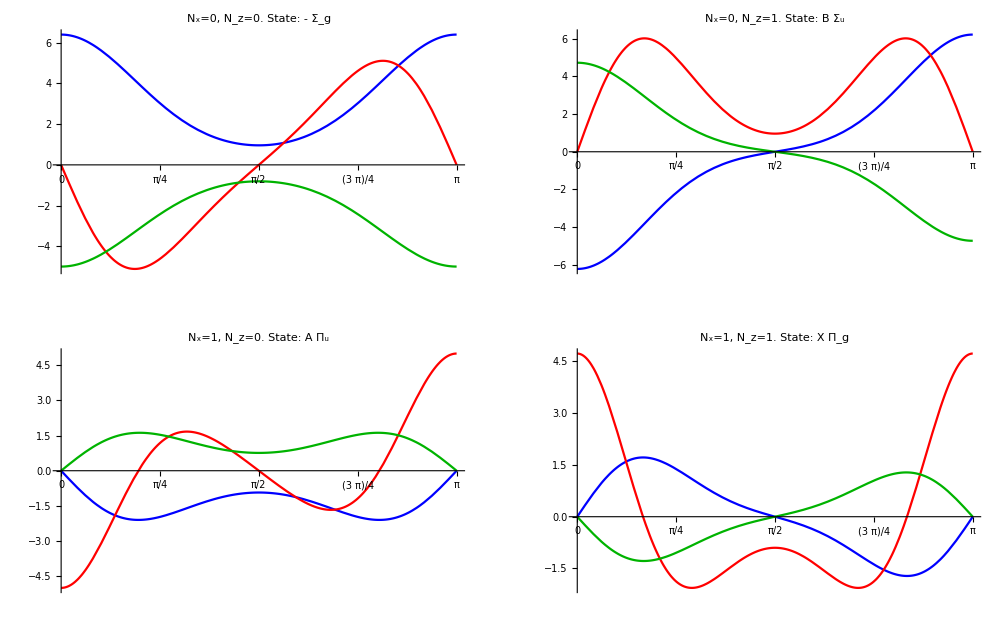

```mathematica
Block[{κ=1.15,b=2.5,c=0.3,a=30},
GraphicsGrid[
Table[
Plot[{
a ⅇ^(-κ a)SFTrestricted[θ,κ,a,b,c,nx,0,nz]
,Evaluate[a ⅇ^(-κ a)Im[SFTderivative[θ,κ,a,b,c,nx,0,nz]]]
,Evaluate[a ⅇ^(-κ a)Im[SFTpy[θ,κ,a,b,c,nx,1,nz]]]
},{θ,0,π/1}
,PlotRange->Full
,PlotLabel->"N_x="<>ToString[nx]<>", N_z="<>ToString[nz]<>". State: "<>Piecewise[{{"X Π_g",2nz+nx==3},{"A Π_u",2nz+nx==1},{"B Σ_u",2nz+nx==2},{"- Σ_g",2nz+nx==0}}]
,PlotStyle->{Blue,Red,Darker[Green,0.3]}
,Ticks->{π/4 Range[0,4],Automatic}
]
,{nx,0,1},{nz,0,1}]
,ImageSize->1000,PlotLabel->"SFT(0) and -ⅈ(∂SFT)/(∂p_o)(0) at N_y=0,  -ⅈ(∂SFT)/(∂p_y)(0) at N_y=1. κ=1.15, b=2.5, c=0.3, a=30"]
]
```